# Aeronet Aerosol optical properties retrievals

AERONET Retrievals AOD Distribution (AERORAD) script is used to retrieve scatter plot of Aerosol Optical Depth (AOD) and Angstrom Exponent (AE) from AERONET data.

It is also retrieved the time series of AOD and mean daily AOD measured by AERONET sunphotometer for the wavelenghts of 532 and 355 nm.

as input are used:
- the 1.5 or level 2.0 raw data downloaded at AERONET website from optical properties
- the local site name as a string (Ex:localsite = "Alta Floresta", localsite = "São Paulo", localsite = "Campo Grande", etc)
- the number position to be read (Ex: filenumber = 1, filenumber = 2, filenumber = 3, etc)

as output is exported ascii files with mean daily AOD, the percentage of data at each graphic quadrant (indication of aerosol type on the AOD vs. AE graphics), the AOD vs. AE scatterplot, AOD and mean daily AOD time series.

AERORAD_v2014_01 script was developed by Dr. Fabio Lopes and the AERORAD_v2016_01 was updated on December 2016 in order to calculate the AOD for 355 nm too.

Feel free to make changes and adaptation,although, don't forget the mention or cite the authors

## Initial Setup Directory and information

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
files=FileNames["*.lev*"]
localsite="Sao Paulo";
sigalgaritmos=2;
filenumber=1;
data=Import[files⟦filenumber⟧,"Table"];
```

{160801_160930_Sao_Paulo.lev15}

```mathematica
std[x_]:=Which[(Length[x]==1),0.2x⟦1⟧,True,StandardDeviation[x]]
```

## Organizing data - String to expression data

```mathematica
dataaot=Drop[data,5];
(*dataaot2=Drop[dataaot1,{267}];
dataaot3=Drop[dataaot2,{9818,10361}];
dataaot4=Drop[dataaot3,{10462-543-2}];
dataaot5=Drop[dataaot4,{10471-543-3}];
dataaot6=Drop[dataaot5,{10512-543-4}];
dataaot7=Drop[dataaot6,{10549-543-5}];
dataaot=Drop[dataaot7,{10596-543-6}];*)
```

```mathematica
len=Length[dataaot];
```

```mathematica
dataaodtotal=Flatten[Table[StringSplit[dataaot⟦i⟧,","],{i,1,len}],1];
```

```mathematica
aod675aux=ToExpression[Table[dataaodtotal⟦i⟧⟦7⟧,{i,1,len}]];
aod500aux=ToExpression[Table[dataaodtotal⟦i⟧⟦13⟧,{i,1,len}]];
aod440aux=ToExpression[Table[dataaodtotal⟦i⟧⟦16⟧,{i,1,len}]];
aod380aux=ToExpression[Table[dataaodtotal⟦i⟧⟦18⟧,{i,1,len}]];
aod340aux=ToExpression[Table[dataaodtotal⟦i⟧⟦19⟧,{i,1,len}]];
```

```mathematica
julidayaux=ToExpression[Table[dataaodtotal⟦i⟧⟦3⟧,{i,1,len}]];
```

```mathematica
timeaux=ToExpression[Table[StringSplit[dataaodtotal⟦i⟧⟦2⟧,":"],{i,1,len}]];
```

```mathematica
dateaux=ToExpression[Table[Reverse[StringSplit[dataaodtotal⟦i⟧⟦1⟧,":"]],{i,1,len}]];
```

```mathematica
datetimeaux=ToExpression[Table[Join[Reverse[StringSplit[dataaodtotal⟦i⟧⟦1⟧,":"]],StringSplit[dataaodtotal⟦i⟧⟦2⟧,":"]],{i,1,len}]];
```

```mathematica
datename=Table[Reverse[StringSplit[dataaodtotal⟦i⟧⟦1⟧,":"]],{i,1,len}];
timename=Table[StringSplit[dataaodtotal⟦i⟧⟦2⟧,":"],{i,1,len}];
```

## AOD for several λ - separated by Julian day

```mathematica
jdsplit=SplitBy[IntegerPart[julidayaux]];
```

```mathematica
lenjdsplit=Length[jdsplit];
```

```mathematica
leneach=Table[Length[jdsplit⟦i⟧],{i,1,lenjdsplit}];
```

```mathematica
reallen=Array[t,lenjdsplit];
```

```mathematica
interac=0;
interac1=0;
For[i=1,i≤lenjdsplit,

Do[reallen⟦i⟧=leneach⟦i⟧+interac];
Do[interac=reallen⟦i⟧];

Do[  aod675all=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[  aod500all=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[  aod440all=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[  aod380all=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[  aod340all=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[  timeall=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[  ae532=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[  ae355=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[  aod532=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[  aod355=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[ resp532=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[ resp355=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[ date=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[ datetime=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[ datename2=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[timename2=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[datetimeaod532=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[datetimeae532=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[timeaod532=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[datetimeaod355=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[datetimeae355=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];
Do[timeaod355=Table[Array[t,leneach⟦i⟧],{i,1,lenjdsplit}]];

i++];
```

```mathematica
interac1=0;
For[i=1,i≤lenjdsplit,

Do[aod675all⟦i⟧=Table[aod675aux⟦i⟧,{i,1+interac1,reallen⟦i⟧}]];
Do[aod500all⟦i⟧=Table[aod500aux⟦i⟧,{i,1+interac1,reallen⟦i⟧}]];
Do[aod440all⟦i⟧=Table[aod440aux⟦i⟧,{i,1+interac1,reallen⟦i⟧}]];
Do[aod380all⟦i⟧=Table[aod380aux⟦i⟧,{i,1+interac1,reallen⟦i⟧}]];
Do[aod340all⟦i⟧=Table[aod340aux⟦i⟧,{i,1+interac1,reallen⟦i⟧}]];
Do[timeall⟦i⟧=Table[timeaux⟦i⟧,{i,1+interac1,reallen⟦i⟧}]];
Do[date⟦i⟧=Table[dateaux⟦i⟧,{i,1+interac1,reallen⟦i⟧}]];
Do[datetime⟦i⟧=Table[datetimeaux⟦i⟧,{i,1+interac1,reallen⟦i⟧}]];
Do[datename2⟦i⟧=Table[datename⟦i⟧,{i,1+interac1,reallen⟦i⟧}]];
Do[timename2⟦i⟧=Table[timename⟦i⟧,{i,1+interac1,reallen⟦i⟧}]];

Do[interac1=reallen⟦i⟧];

i++];
```

## Angstrom Exponent using τ_440, τ_675, AOD_532 and τ_340, τ_440, AOD_380

```mathematica
For[i=1,i≤lenjdsplit,

Do[ae532⟦i⟧=Table[-Log[(aod440all⟦i⟧⟦j⟧)/(aod675all⟦i⟧⟦j⟧)]/Log[440/675],{j,1,leneach⟦i⟧}];];

Do[ae355⟦i⟧=Table[-Log[(aod340all⟦i⟧⟦j⟧)/(aod440all⟦i⟧⟦j⟧)]/Log[340/440],{j,1,leneach⟦i⟧}];];

(*Do[aod532⟦i⟧=Table[aod500all⟦i⟧⟦j⟧ (532/500)^(-ae⟦i⟧⟦j⟧),{j,1,leneach⟦i⟧}];];*)


Do[aod532⟦i⟧=SetAccuracy[Table[aod500all⟦i⟧⟦j⟧ (532/500)^(-ae532⟦i⟧⟦j⟧),{j,1,leneach⟦i⟧}],5];];

Do[aod355⟦i⟧=SetAccuracy[Table[aod380all⟦i⟧⟦j⟧ (355/380)^(-ae355⟦i⟧⟦j⟧),{j,1,leneach⟦i⟧}],5];];

Do[resp532⟦i⟧=Table[{timeall⟦i⟧⟦j⟧⟦1⟧,timeall⟦i⟧⟦j⟧⟦2⟧,timeall⟦i⟧⟦j⟧⟦3⟧, aod532⟦i⟧⟦j⟧, ae532⟦i⟧⟦j⟧},{j,1,leneach⟦i⟧}];];

Do[resp355⟦i⟧=Table[{timeall⟦i⟧⟦j⟧⟦1⟧,timeall⟦i⟧⟦j⟧⟦2⟧,timeall⟦i⟧⟦j⟧⟦3⟧, aod355⟦i⟧⟦j⟧, ae355⟦i⟧⟦j⟧},{j,1,leneach⟦i⟧}];];

Do[datetimeaod532⟦i⟧=Table[{datetime⟦i⟧⟦j⟧, aod532⟦i⟧⟦j⟧},{j,1,leneach⟦i⟧}];];

Do[timeaod532⟦i⟧=Table[{timeall⟦i⟧⟦j⟧, aod532⟦i⟧⟦j⟧},{j,1,leneach⟦i⟧}];];

Do[datetimeae532⟦i⟧=Table[{datetime⟦i⟧⟦j⟧, ae532⟦i⟧⟦j⟧},{j,1,leneach⟦i⟧}];];

Do[datetimeaod355⟦i⟧=Table[{datetime⟦i⟧⟦j⟧, aod355⟦i⟧⟦j⟧},{j,1,leneach⟦i⟧}];];

Do[timeaod355⟦i⟧=Table[{timeall⟦i⟧⟦j⟧, aod355⟦i⟧⟦j⟧},{j,1,leneach⟦i⟧}];];

Do[datetimeae355⟦i⟧=Table[{datetime⟦i⟧⟦j⟧, ae355⟦i⟧⟦j⟧},{j,1,leneach⟦i⟧}];];



i++];
```

## Plot of Angstrom Exponent vs. AOD_532

```mathematica
aod532aux=Flatten[aod532,1];
ae532aux=Flatten[ae532,1];
aodae532=Table[{aod532aux⟦i⟧,ae532aux⟦i⟧},{i,1,Length[ae532aux]}];
```

```mathematica
aod355aux=Flatten[aod355,1];
ae355aux=Flatten[ae355,1];
aodae355=Table[{aod355aux⟦i⟧,ae355aux⟦i⟧},{i,1,Length[ae355aux]}];
```

### Medians and Standard Deviation

```mathematica
medianaod532=Median[aod532aux]
medianae532=Median[ae532aux]
stdeviationmedianaod532=MedianDeviation[aod532aux]//N;
stdeviationmedianae532=MedianDeviation[ae532aux];
```

0.1753

1.49015

```mathematica
medianaod355=Median[aod355aux]
medianae355=Median[ae355aux]
stdeviationmedianaod355=MedianDeviation[aod355aux]//N;
stdeviationmedianae355=MedianDeviation[ae355aux];
```

0.282

0.843385

### Means and Standard Deviation

```mathematica
meanaod532 = Mean[aod532aux]
stdeviationaod532 = StandardDeviation[aod532aux]
meanae532 = Mean[ae532aux]
stdeviationae532 = StandardDeviation[ae532aux]
```

0.2201

0.1514

1.47356

0.187718

```mathematica
meanaod355 = Mean[aod355aux]
stdeviationaod355 = StandardDeviation[aod355aux]
meanae355 = Mean[ae355aux]
stdeviationae355 = StandardDeviation[ae355aux]
```

0.3515

0.2258

0.806645

0.240947

## Sectors - Angstrom and AOD for 355 and 532 nm

```mathematica
sector1532=Select[aodae532,#⟦1⟧≤ meanaod532&&#⟦2⟧≥ meanae532&];
sector2532=Select[aodae532,#⟦1⟧≥meanaod532&&#⟦2⟧≥meanae532&];
sector3532=Select[aodae532,#⟦1⟧≤meanaod532&&#⟦2⟧≤meanae532&];
sector4532=Select[aodae532,#⟦1⟧≥meanaod532&&#⟦2⟧≤ meanae532&];
```

```mathematica
porcentagesector1532=SetAccuracy[Length[sector1532]/Length[aodae532],4]
porcentagesector2532=SetAccuracy[Length[sector2532]/Length[aodae532],4]
porcentagesector3532=SetAccuracy[Length[sector3532]/Length[aodae532],4]
porcentagesector4532=SetAccuracy[Length[sector4532]/Length[aodae532],4]
```

0.373

0.198

0.299

0.13

```mathematica
sector1355=Select[aodae355,#⟦1⟧≤ meanaod355&&#⟦2⟧≥ meanae355&];
sector2355=Select[aodae355,#⟦1⟧≥meanaod355&&#⟦2⟧≥meanae355&];
sector3355=Select[aodae355,#⟦1⟧≤meanaod355&&#⟦2⟧≤meanae355&];
sector4355=Select[aodae355,#⟦1⟧≥meanaod355&&#⟦2⟧≤ meanae355&];
```

```mathematica
porcentagesector1355=SetAccuracy[Length[sector1355]/Length[aodae355],4]
porcentagesector2355=SetAccuracy[Length[sector2355]/Length[aodae355],4]
porcentagesector3355=SetAccuracy[Length[sector3355]/Length[aodae355],4]
porcentagesector4355=SetAccuracy[Length[sector4355]/Length[aodae355],4]
```

0.334

0.222

0.336

0.108

```mathematica
resp532={"Percentage sector I",porcentagesector1532,"","Percentage sector II",porcentagesector2532,"","Percentage sector III",porcentagesector3532,"","Percentage sector IV",porcentagesector4532};
```

```mathematica
resp532={"Percentage sector I",porcentagesector1355,"","Percentage sector II",porcentagesector2355,"","Percentage sector III",porcentagesector3355,"","Percentage sector IV",porcentagesector4355};
```

## AOD_532 vs. AE plots - calculations

```mathematica
medianaodplot532=Table[{meanaod532,i},{i,0,5,0.2}];
medianaeplot532=Table[{i,meanae532},{i,0,5,0.2}];
medianaodplot1532=Table[{meanaod532-stdeviationaod532,i},{i,0,5,0.2}];
medianaeplot1532=Table[{i,meanae532-stdeviationae532},{i,0,5,0.2}];
medianaodplot2532=Table[{meanaod532+stdeviationaod532,i},{i,0,5,0.2}];
medianaeplot2532=Table[{i,meanae532+stdeviationae532},{i,0,5,0.2}];
```

```mathematica
medianaodplot355=Table[{meanaod355,i},{i,0,5,0.2}];
medianaeplot355=Table[{i,meanae355},{i,0,5,0.2}];
medianaodplot1355=Table[{meanaod355-stdeviationaod355,i},{i,0,5,0.2}];
medianaeplot1355=Table[{i,meanae355-stdeviationae355},{i,0,5,0.2}];
medianaodplot2355=Table[{meanaod355+stdeviationaod355,i},{i,0,5,0.2}];
medianaeplot2355=Table[{i,meanae355+stdeviationae355},{i,0,5,0.2}];
```

```mathematica
(*medianplot=ListPlot[{medianaodplot,medianaeplot,medianaodplot1,medianaeplot1,medianaodplot2,medianaeplot2},Joined->{True, True},PlotRange->{{0,5},{0,2.0}}, Frame->True,PlotStyle->{{Dashed, RGBColor[0,0.1,1],Thickness[0.004]},{Dashed, RGBColor[0,0.1,1],Thickness[0.004]},{ RGBColor[0,0.1,1],Thickness[0.004]},{ RGBColor[0,0.1,1],Thickness[0.004]},{ RGBColor[0,0.1,1],Thickness[0.004]},{ RGBColor[0,0.1,1],Thickness[0.004]}},FrameStyle->Directive[30,Thickness[0.0027]]]*)
```

```mathematica
medianplot532=ListPlot[{medianaodplot532,medianaeplot532},Joined->{True, True},PlotRange->{{0,5},{0,3.0}}, Frame->True,PlotStyle->{{Dashed, RGBColor[0.07,0.9,0],Thickness[0.004]},{Dashed, RGBColor[0.07,0.9,0],Thickness[0.004]},{ RGBColor[0,0.1,1],Thickness[0.004]},{ RGBColor[0,0.1,1],Thickness[0.004]}},FrameStyle->Directive[30,Thickness[0.0027]]];
```

```mathematica
medianplot2532=ListPlot[{medianaodplot532,medianaeplot532},Joined->{True, True},PlotRange->{{0,5},{0,3.0}}, Frame->True,PlotStyle->{{Dashed,GrayLevel[0.5],Thickness[0.005]},{Dashed,GrayLevel[0.5],Thickness[0.005]},{ RGBColor[0,0.1,1],Thickness[0.004]},{ RGBColor[0,0.1,1],Thickness[0.004]}},FrameStyle->Directive[30,Thickness[0.0027]]];
```

```mathematica
medianplot355=ListPlot[{medianaodplot355,medianaeplot355},Joined->{True, True},PlotRange->{{0,5},{0,3.0}}, Frame->True,PlotStyle->{{Dashed, RGBColor[0.75,0.25,1],Thickness[0.004]},{Dashed, RGBColor[0.75,0.25,1],Thickness[0.004]},{ RGBColor[0,0.1,1],Thickness[0.004]},{ RGBColor[0,0.1,1],Thickness[0.004]}},FrameStyle->Directive[30,Thickness[0.0027]]];
```

```mathematica
medianplot2355=ListPlot[{medianaodplot355,medianaeplot355},Joined->{True, True},PlotRange->{{0,5},{0,3.0}}, Frame->True,PlotStyle->{{Dashed,GrayLevel[0.5],Thickness[0.005]},{Dashed,GrayLevel[0.5],Thickness[0.005]},{ RGBColor[0,0.1,1],Thickness[0.004]},{ RGBColor[0,0.1,1],Thickness[0.004]}},FrameStyle->Directive[30,Thickness[0.0027]]];
```

## Adjusting names for plottings and for exporting files

```mathematica
day=Array[t,lenjdsplit];
month=Array[t,lenjdsplit];
year=Array[t,lenjdsplit];
initialhour=Array[t,lenjdsplit];
initialmin=Array[t,lenjdsplit];
finalhour=Array[t,lenjdsplit];
finalmin=Array[t,lenjdsplit];
```

```mathematica
For[i=1,i≤lenjdsplit,

Do[day⟦i⟧=datename2⟦i⟧⟦1⟧⟦3⟧];
Do[month⟦i⟧=datename2⟦i⟧⟦1⟧⟦2⟧];
Do[year⟦i⟧=datename2⟦i⟧⟦1⟧⟦1⟧];
Do[initialhour⟦i⟧=timename2⟦i⟧⟦1⟧⟦1⟧];
Do[initialmin⟦i⟧=timename2⟦i⟧⟦1⟧⟦1⟧];
Do[finalhour⟦i⟧=timename2⟦i⟧⟦leneach⟦i⟧⟧⟦1⟧];
Do[finalmin⟦i⟧=timename2⟦i⟧⟦leneach⟦i⟧⟧⟦2⟧];
i++];
```

```mathematica
dateexp01=DateString[{ToExpression[year⟦1⟧],ToExpression[month⟦1⟧]},{"Year"}];
dateexp02=DateString[{ToExpression[year⟦1⟧],ToExpression[month⟦1⟧]},{"MonthName"}];
dateexp03=DateString[{ToExpression[year⟦1⟧],ToExpression[month⟦-1⟧]},{"MonthName"}];
dateexp=StringJoin[dateexp01,"_",dateexp02,"_",dateexp03]
localsite2=StringTake[files⟦filenumber⟧,{15,-7}];
stringlevel=StringTake[files⟦filenumber⟧,-5];
plotlabelgraphics=StringJoin[localsite, " AERONET Station ", dateexp02,"-",dateexp03," ",dateexp01];
```

2016_August_September

```mathematica
meanaodstring532=StringJoin["OverBar[AOD]_532 = ",ToString[SetPrecision[meanaod532,sigalgaritmos]]," ± ",ToString[SetPrecision[stdeviationaod532,sigalgaritmos-1]]];
meanaestring532=StringJoin["OverBar[AE]_532= ",ToString[SetPrecision[meanae532,sigalgaritmos+1]]," ± ",ToString[SetPrecision[stdeviationae532,sigalgaritmos]]];
```

```mathematica
meanaodstring355=StringJoin["OverBar[AOD]_355 = ",ToString[SetPrecision[meanaod355,sigalgaritmos]]," ± ",ToString[SetPrecision[stdeviationaod355,sigalgaritmos]]];
meanaestring355=StringJoin["OverBar[AE]_355= ",ToString[SetPrecision[meanae355,sigalgaritmos+1]]," ± ",ToString[SetPrecision[stdeviationae355,sigalgaritmos]]];
```

## AOD_532 vs. AE plots

```mathematica
aodaegraph532=ListPlot[aodae532,Joined->False,PlotRange->{{0,4},{0,2.5}}, Frame->True,FrameStyle->Directive[25,Thickness[0.0027]],PlotStyle-> {RGBColor[0,0,0.1],PointSize[.01],Opacity[0.7]},PlotLabel->Style[plotlabelgraphics,31],FrameLabel->{"AOD at 532 nm","Angstrom Exponent"},BaseStyle->{FontFamily->"Arial Black",FontSize->20,Bold},LabelStyle->{FontFamily->"Arial",FontSize->25,Bold},TicksStyle->Black,

Epilog->{Inset[StyleForm[meanaodstring532,FontSize->27,FontFamily->"Arial Black",FontWeight->"Bold"],{3.35,2.3}],Inset[StyleForm[meanaestring532,FontSize->27,FontFamily->"Arial Black",FontWeight->"Bold"],{3.40,2.0}]},

AspectRatio->0.35,ImageSize->1100];
```

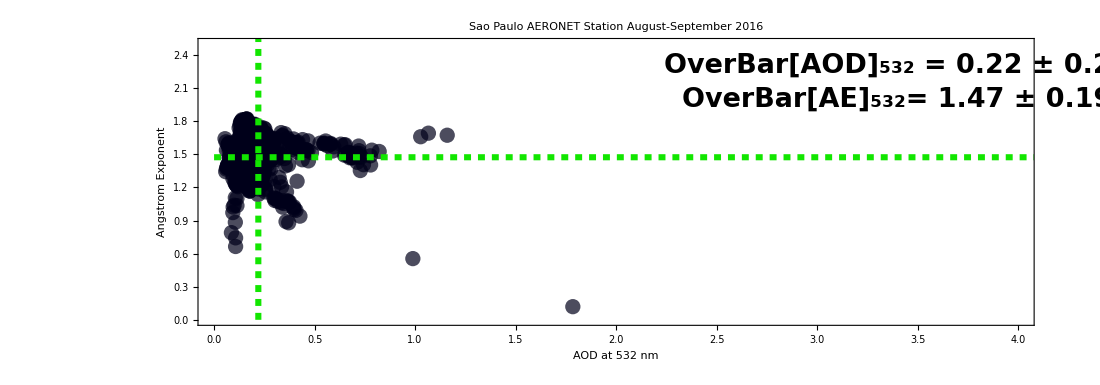

```mathematica
aodaefinalplot532=Show[aodaegraph532,medianplot532]
```

```mathematica
aodaegraph355=ListPlot[aodae355,Joined->False,PlotRange->{{0,4},{0,2.5}}, Frame->True,FrameStyle->Directive[25,Thickness[0.0027]],PlotStyle-> {RGBColor[0,0,0.1],PointSize[.01],Opacity[0.7]},PlotLabel->Style[plotlabelgraphics,31],FrameLabel->{"AOD at 355 nm","Angstrom Exponent"},BaseStyle->{FontFamily->"Arial Black",FontSize->20,Bold},LabelStyle->{FontFamily->"Arial",FontSize->25,Bold},TicksStyle->Black,

Epilog->{Inset[StyleForm[meanaodstring355,FontSize->27,FontFamily->"Arial Black",FontWeight->"Bold"],{3.35,2.3}],Inset[StyleForm[meanaestring355,FontSize->27,FontFamily->"Arial Black",FontWeight->"Bold"],{3.40,2.0}]},

AspectRatio->0.35,ImageSize->1100];
```

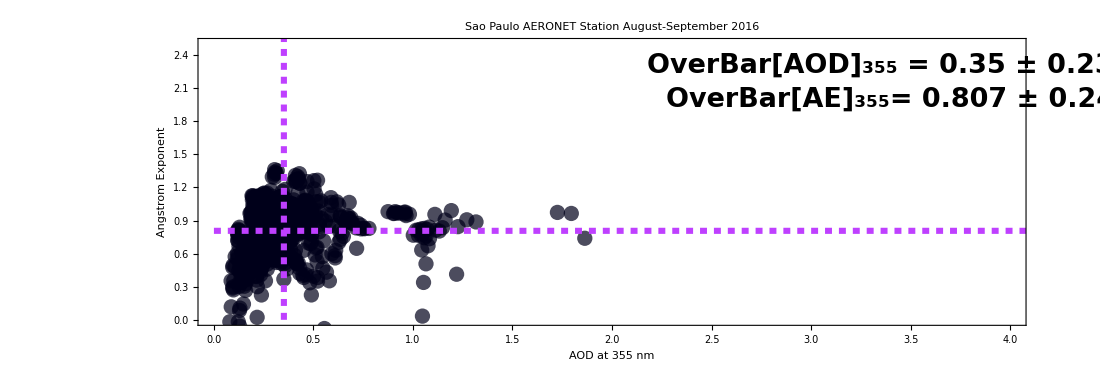

```mathematica
aodaefinalplot355=Show[aodaegraph355,medianplot355]
```

## AOD_532 vs. Date plots

```mathematica
datetimeaodaux532=Flatten[datetimeaod532,1];
```

```mathematica
datetimeaeaux532=Flatten[datetimeae532,1];
```

```mathematica
plotAODtotal532=DateListPlot[Tooltip[datetimeaodaux532],Joined->True,PlotRange->{{{2016,08,01,00,0},{2016,08,31,24,0}},{0,2}}, Frame->True,FrameStyle->Directive[25,Thickness[0.0027]],PlotStyle-> {GrayLevel[0],PointSize[0.30],Opacity[0.9]},PlotMarkers->{•,17},PlotLabel->Style[plotlabelgraphics,31],FrameLabel->{"Date","AOD at 532 nm"},BaseStyle->{FontFamily->"Arial Black",FontSize->20,Bold},LabelStyle->{FontFamily->"Arial",FontSize->25,Bold},TicksStyle->Black,DateTicksFormat->{"Year","/","MonthNameShort","/","Day"},Filling->None,GridLines->{    {{{2011,9,02,15,0},White},{{2012,9,15,15,0},White
}},{{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}}}},
Epilog->{Inset[StyleForm[meanaodstring532,FontSize->27,FontFamily->"Arial Black",FontWeight->"Bold"],{{2012,07,18},3.7}]},
                           AspectRatio-> 0.35, ImageSize->1000];
```

## AOD_355 vs. Date plots

```mathematica
datetimeaodaux355=Flatten[datetimeaod355,1];
```

```mathematica
datetimeaeaux355=Flatten[datetimeae355,1];
```

```mathematica
plotAODtotal355=DateListPlot[Tooltip[datetimeaodaux355],Joined->True,PlotRange->{{{2016,08,01,00,0},{2016,08,31,24,0}},{0,2}}, Frame->True,FrameStyle->Directive[25,Thickness[0.0027]],PlotStyle-> {GrayLevel[0],PointSize[0.30],Opacity[0.9]},PlotMarkers->{•,17},PlotLabel->Style[plotlabelgraphics,31],FrameLabel->{"Date","AOD at 532 nm"},BaseStyle->{FontFamily->"Arial Black",FontSize->20,Bold},LabelStyle->{FontFamily->"Arial",FontSize->25,Bold},TicksStyle->Black,DateTicksFormat->{"Year","/","MonthNameShort","/","Day"},Filling->None,GridLines->{    {{{2011,9,02,15,0},White},{{2012,9,15,15,0},White
}},{{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}}}},
Epilog->{Inset[StyleForm[meanaodstring355,FontSize->27,FontFamily->"Arial Black",FontWeight->"Bold"],{{2012,07,18},3.7}]},
                           AspectRatio-> 0.35, ImageSize->1000];
```

## AOD_532 and AOD_355 hourly mean vs. date plot - calculations

```mathematica
countsplit=Table[Table[timeall⟦i⟧⟦j⟧⟦1⟧,{j,1,Length[timeall⟦i⟧]}],{i,1,Length[timeall]}];(*Selecionando apenas os valores das horas hora*)
```

```mathematica
splithour=Table[Split[countsplit⟦i⟧],{i,1,Length[countsplit]}];(*Separando os horários iguais para realizar medias*)
```

```mathematica
leneachsplithour=Table[Table[Length[splithour⟦i⟧⟦j⟧],{j,1,Length[splithour⟦i⟧]}],{i,1,Length[splithour]}];(*tamanho de cada vetor horario*)
```

```mathematica
aodsepar532=Table[Table[Table[timeaod532⟦i⟧⟦k⟧⟦2⟧,{k,1,leneachsplithour⟦i⟧⟦j⟧}],{j,1,Length[leneachsplithour⟦i⟧]}],{i,1,Length[countsplit]}]; (*separando os valores de AOD para cada vetor horário*)
```

```mathematica
aodsepar355=Table[Table[Table[timeaod355⟦i⟧⟦k⟧⟦2⟧,{k,1,leneachsplithour⟦i⟧⟦j⟧}],{j,1,Length[leneachsplithour⟦i⟧]}],{i,1,Length[countsplit]}] ;(*separando os valores de AOD para cada vetor horário*)
```

```mathematica
aodhourly532=Table[Table[Mean[aodsepar532⟦i⟧⟦j⟧],{j,1,Length[leneachsplithour⟦i⟧]}],{i,1,Length[countsplit]}];(*valores medios de AOD em cada hora*)
stdevaodhourly532=Table[Table[std[aodsepar532⟦i⟧⟦j⟧],{j,1,Length[leneachsplithour⟦i⟧]}],{i,1,Length[countsplit]}];
```

```mathematica
aodhourly355=Table[Table[Mean[aodsepar355⟦i⟧⟦j⟧],{j,1,Length[leneachsplithour⟦i⟧]}],{i,1,Length[countsplit]}];(*valores medios de AOD em cada hora*)
stdevaodhourly355=Table[Table[std[aodsepar355⟦i⟧⟦j⟧],{j,1,Length[leneachsplithour⟦i⟧]}],{i,1,Length[countsplit]}];
```

```mathematica
firsthour=Table[Table[splithour⟦i⟧⟦j⟧⟦1⟧,{j,1,Length[leneachsplithour⟦i⟧]}],{i,1,Length[countsplit]}];
```

```mathematica
datasepa=Table[Table[Flatten[{date⟦i⟧⟦1⟧,firsthour⟦i⟧⟦j⟧}],{j,1,Length[leneachsplithour⟦i⟧]}],{i,1,Length[countsplit]}];
```

```mathematica
datemeantimeaod532=Table[Table[{datasepa⟦i⟧⟦j⟧,aodhourly532⟦i⟧⟦j⟧},{j,1,Length[leneachsplithour⟦i⟧]}],{i,1,Length[countsplit]}];
```

```mathematica
datemeantimeaod355=Table[Table[{datasepa⟦i⟧⟦j⟧,aodhourly355⟦i⟧⟦j⟧},{j,1,Length[leneachsplithour⟦i⟧]}],{i,1,Length[countsplit]}];
```

```mathematica
datemeantimeaodaux532=Flatten[datemeantimeaod532,1];
```

```mathematica
datemeantimeaodaux355=Flatten[datemeantimeaod355,1];
```

## AOD_532 and AOD_355 daily mean vs. date plot - calculations

```mathematica
meandailyaod532=Table[{ date⟦i⟧⟦1⟧,  Mean[Flatten[aodsepar532⟦i⟧]],std[Flatten[aodsepar532⟦i⟧]]},{i,1,Length[aodsepar532]}];
```

```mathematica
meandailyaod355=Table[{ date⟦i⟧⟦1⟧,  Mean[Flatten[aodsepar355⟦i⟧]],std[Flatten[aodsepar355⟦i⟧]]},{i,1,Length[aodsepar355]}];
```

## AOD_532 hourly mean vs. date plot

```mathematica
plotmeanAOD532=DateListPlot[Tooltip[datemeantimeaodaux532],Joined->True,PlotRange->{{{2016,08,01,00,0},{2016,08,31,24,0}},{0,2}}, Frame->True,FrameStyle->Directive[25,Thickness[0.0027]],PlotStyle-> {GrayLevel[0],PointSize[0.30],Opacity[0.9]},PlotMarkers->{•,17},PlotLabel->Style[plotlabelgraphics,31],FrameLabel->{"Date","AOD at 532 nm"},BaseStyle->{FontFamily->"Arial Black",FontSize->20,Bold},LabelStyle->{FontFamily->"Arial",FontSize->25,Bold},TicksStyle->Black,DateTicksFormat->{"Year","/","MonthNameShort","/","Day"},Filling->None,GridLines->{    {{{2011,9,02,15,0},White},{{2012,9,15,15,0},White
}},{{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}}}},
Epilog->{Inset[StyleForm[meanaodstring532,FontSize->27,FontFamily->"Arial Black",FontWeight->"Bold"],{{2012,07,18},3.7}]},
                          AspectRatio->0.35, ImageSize->1000];
```

```mathematica
plotmeanAOD355=DateListPlot[Tooltip[datemeantimeaodaux355],Joined->True,PlotRange->{{{2016,08,01,00,0},{2016,08,31,24,0}},{0,2}}, Frame->True,FrameStyle->Directive[25,Thickness[0.0027]],PlotStyle-> {GrayLevel[0],PointSize[0.30],Opacity[0.9]},PlotMarkers->{•,17},PlotLabel->Style[plotlabelgraphics,31],FrameLabel->{"AOD at 355 nm","Angstrom Exponent"},BaseStyle->{FontFamily->"Arial Black",FontSize->20,Bold},LabelStyle->{FontFamily->"Arial",FontSize->25,Bold},TicksStyle->Black,DateTicksFormat->{"Year","/","MonthNameShort","/","Day"},Filling->None,GridLines->{    {{{2011,9,02,15,0},White},{{2012,9,15,15,0},White
}},{{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}},{0,{Darker[Gray],Dashed,Thickness[0.004]}}}},
Epilog->{Inset[StyleForm[meanaodstring355,FontSize->27,FontFamily->"Arial Black",FontWeight->"Bold"],{{2012,07,18},3.7}]},
                          AspectRatio->0.35, ImageSize->1000];
```

## Exporting individual files - AOD, AR and date

```mathematica
aoddir532=CreateDirectory[ToString[year⟦1⟧]<>"_AOD532_results_"<>stringlevel]
aoddir355=CreateDirectory[ToString[year⟦1⟧]<>"_AOD355_results_"<>stringlevel];
```

CreateDirectory::filex: N:\2017-2018\board_task_02\40-paper03-RAPEL_GRASP\data_analysis\AERONET\160801_160930_Sao_Paulo\2016_AOD532_results_lev15 already exists.

$Failed

CreateDirectory::filex: N:\2017-2018\board_task_02\40-paper03-RAPEL_GRASP\data_analysis\AERONET\160801_160930_Sao_Paulo\2016_AOD355_results_lev15 already exists.

```mathematica
Export[ToFileName[aoddir532,dateexp<>"_"<>"AODvsAE_scatterplot_532nm"<>"_"<>localsite2<>".tiff"],aodaefinalplot532];
Export[ToFileName[aoddir532,dateexp<>"_"<>"AOD_timeseries_532nm"<>"_"<>localsite2<>".tiff"],plotAODtotal532];
Export[ToFileName[aoddir532,dateexp<>"_"<>"AOD_timeseries"<>"_mean_532nm"<>"_"<>localsite2<>".tiff"],plotmeanAOD532];
Export[ToFileName[aoddir532,dateexp<>"_"<>"AODAE_sectoranalysis_532nm"<>"_"<>localsite2<>".dat"],resp532];
```

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AODvsAE_scatterplot_532nm_Sao_Paulo.tiff].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AODvsAE_scatterplot_532nm_Sao_Paulo.tiff] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AOD_timeseries_532nm_Sao_Paulo.tiff].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AOD_timeseries_532nm_Sao_Paulo.tiff] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AOD_timeseries_mean_532nm_Sao_Paulo.tiff].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AOD_timeseries_mean_532nm_Sao_Paulo.tiff] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AODAE_sectoranalysis_532nm_Sao_Paulo.dat].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AODAE_sectoranalysis_532nm_Sao_Paulo.dat] is not a valid file specification.

```mathematica
Export[ToFileName[aoddir355,dateexp<>"_"<>"AODvsAE_scatterplot_355nm"<>"_"<>localsite2<>".tiff"],aodaefinalplot355];
Export[ToFileName[aoddir355,dateexp<>"_"<>"AOD_timeseries_355nm"<>"_"<>localsite2<>".tiff"],plotAODtotal355];
Export[ToFileName[aoddir355,dateexp<>"_"<>"AOD_timeseries_355nm"<>"_mean"<>"_"<>localsite2<>".tiff"],plotmeanAOD355];
Export[ToFileName[aoddir355,dateexp<>"_"<>"AODAE_sectoranalysis_355nm"<>"_"<>localsite2<>".dat"],resp355];
```

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AODvsAE_scatterplot_355nm_Sao_Paulo.tiff].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AODvsAE_scatterplot_355nm_Sao_Paulo.tiff] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AOD_timeseries_355nm_Sao_Paulo.tiff].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AOD_timeseries_355nm_Sao_Paulo.tiff] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AOD_timeseries_355nm_mean_Sao_Paulo.tiff].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AOD_timeseries_355nm_mean_Sao_Paulo.tiff] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AODAE_sectoranalysis_355nm_Sao_Paulo.dat].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AODAE_sectoranalysis_355nm_Sao_Paulo.dat] is not a valid file specification.

```mathematica
SetDirectory[NotebookDirectory[]];
aoddirmean532=CreateDirectory[ToString[year⟦1⟧]<>"_AOD532_media_results_"<>stringlevel];
aoddirmean355=CreateDirectory[ToString[year⟦1⟧]<>"_AOD355_media_results_"<>stringlevel];

Export[ToFileName[aoddirmean532,dateexp<>"_"<>"AOD532_all"<>".dat"],Table[Flatten[datetimeaodaux532⟦i⟧],{i,1,Length[datetimeaodaux532]}] ];
Export[ToFileName[aoddirmean532,dateexp<>"_"<>"AE532_all"<>".dat"],Table[Flatten[datetimeaeaux532⟦i⟧],{i,1,Length[datetimeaeaux532]}] ];
Export[ToFileName[aoddirmean532,dateexp<>"_"<>"AOD532_mean"<>".dat"],Table[Flatten[datemeantimeaodaux532⟦i⟧],{i,1,Length[datemeantimeaodaux532]}] ];
Export[ToFileName[aoddirmean532,dateexp<>"_"<>"AOD532_dailymean"<>".dat"],Table[Flatten[meandailyaod532⟦i⟧],{i,1,Length[meandailyaod532]}] ];

Export[ToFileName[aoddirmean355,dateexp<>"_"<>"AOD355_all"<>".dat"],Table[Flatten[datetimeaodaux355⟦i⟧],{i,1,Length[datetimeaodaux355]}] ];
Export[ToFileName[aoddirmean355,dateexp<>"_"<>"AE355_all"<>".dat"],Table[Flatten[datetimeaeaux355⟦i⟧],{i,1,Length[datetimeaeaux355]}] ];
Export[ToFileName[aoddirmean355,dateexp<>"_"<>"AOD355_mean"<>".dat"],Table[Flatten[datemeantimeaodaux355⟦i⟧],{i,1,Length[datemeantimeaodaux355]}] ];
Export[ToFileName[aoddirmean355,dateexp<>"_"<>"AOD355_dailymean"<>".dat"],Table[Flatten[meandailyaod355⟦i⟧],{i,1,Length[meandailyaod355]}] ];
```

CreateDirectory::filex: N:\2017-2018\board_task_02\40-paper03-RAPEL_GRASP\data_analysis\AERONET\160801_160930_Sao_Paulo\2016_AOD532_media_results_lev15 already exists.

CreateDirectory::filex: N:\2017-2018\board_task_02\40-paper03-RAPEL_GRASP\data_analysis\AERONET\160801_160930_Sao_Paulo\2016_AOD355_media_results_lev15 already exists.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AOD532_all.dat].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AOD532_all.dat] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AE532_all.dat].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AE532_all.dat] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AOD532_mean.dat].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AOD532_mean.dat] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AOD532_dailymean.dat].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AOD532_dailymean.dat] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AOD355_all.dat].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AOD355_all.dat] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AE355_all.dat].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AE355_all.dat] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AOD355_mean.dat].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AOD355_mean.dat] is not a valid file specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[$Failed,2016_August_September_AOD355_dailymean.dat].

Export::chtype: First argument ToFileName[$Failed,2016_August_September_AOD355_dailymean.dat] is not a valid file specification.